To-do: Regular payoff distribution, rolling intrinsic payoff distribution. Show convergence.

Forward price evolution: dF_t=F_t σdW_t, or F_t=F_0 e^(-0.5 σ^2 t+σW_t)

```mathematica
F0=3.;
σ=0.3;
T=3.0/12; (*3 months*)
nsteps=90;
dt=T/nsteps; (*1 day per step*)
nmc=100000;
K=3.1;
```

```mathematica
Wt=FoldList[Plus,0.0Range[nmc],√dt RandomVariate[NormalDistribution[0,1],{nsteps,nmc}]]//Rest;
```

```mathematica
Mean[Wt_[[-1]]]
```

-0.00219744

```mathematica
StandardDeviation[Wt_[[-1]]]
```

0.498391

```mathematica
Ft=F0 Exp[-0.5 σ^2 dt Range[nsteps]+σ Wt];
```

```mathematica
Mean[Ft_[[-1]]]
```

2.99778

```mathematica
payoff[F_]:=Max[F-K,0];
SetAttributes[payoff,Listable];
```

```mathematica
policy[F_]:=If[F>K,1,0];
SetAttributes[policy,Listable];
```

```mathematica
Mean[payoff[Ft_[[-1]]]]
```

0.135147

```mathematica
pv=FinancialDerivative[{"Future","European","Call"},{"StrikePrice"->K,"Expiration"->T},{"CurrentPrice"->F0,"Volatility"->σ,"InterestRate"->0}]
```

0.136676

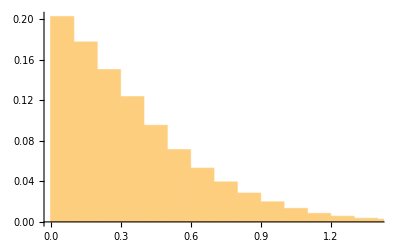

```mathematica
Histogram[Select[payoff[Ft_[[-1]]],Positive],Automatic,"Probability"]
```

How do I code rolling intrinsic?
Take a path

Take path of F and create cpnl:

```mathematica
cpnlPath[Fs_]:=Module[{p=policy[Fs],pstart,pidx,pnl},
pstart=Position[p,1,1,1]//Flatten;
pidx=If[Length[pstart]>0,Accumulate[Prepend[Most[Length/@Split[Drop[p,pstart_[[1]]-1]]],pstart_[[1]]]],{}];
pnl=If[Length[pstart]>0,Append[With[{part=Partition[pidx,2]},{#_[[2]],Fs_[[#_[[1]]]]-Fs_[[#_[[2]]]]}&/@part],{nsteps,payoff[Fs_[[pidx//Last]]]}],{{nsteps,0}}];
{pnl_[[All,1]],Accumulate[pnl_[[All,2]]]}ᵀ]
```

```mathematica
res=cpnlPath/@Transpose[Ft];
```

InterpolatingFunction::dmval: Input value {1.00182} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

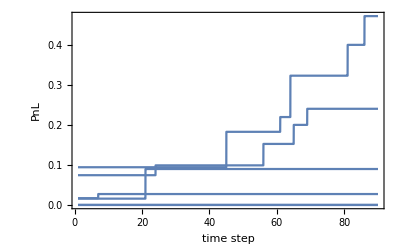

```mathematica
Plot[Interpolation[res_[[#]],InterpolationOrder->0][x]&/@{1,5,10,14,18, 30},{x,1,90},PlotRange->All,Frame->True,FrameLabel->{"time step","PnL"},LabelStyle->Medium]
```

```mathematica
Mean[res_[[All,-1,-1]]]
```

0.136611

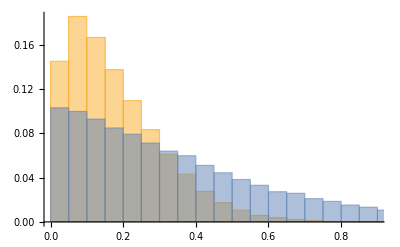

```mathematica
Histogram[{Select[res_[[All,-1,-1]],Positive],Select[payoff[Ft_[[-1]]],Positive]},Automatic,"Probability",LabelStyle->Medium]
```

```mathematica
StandardDeviation[Select[payoff[Ft_[[-1]]],Positive]]
```

0.286375

```mathematica
StandardDeviation[Select[res_[[All,-1,-1]],Positive]]
```

0.126705

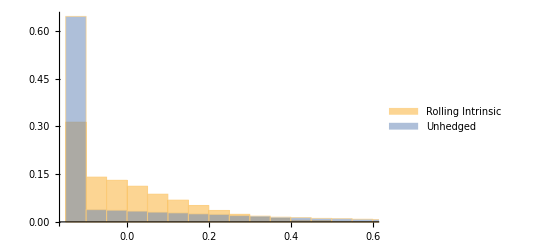

```mathematica
Histogram[{res_[[All,-1,-1]],payoff[Ft_[[-1]]]}-pv,Automatic,"Probability",LabelStyle->Medium,ChartLegends->{"Rolling Intrinsic","Unhedged"}]
```

```mathematica
StandardDeviation[payoff[Ft_[[-1]]]]
```

0.250647

```mathematica
StandardDeviation[res_[[All,-1,-1]]]
```

0.137137